```mathematica
exponentialdata=Table[ⅇ^(0.5x),{x,0,100}]
```

{1.,1.64872,2.71828,4.48169,7.38906,12.1825,20.0855,33.1155,54.5982,90.0171,148.413,244.692,403.429,665.142,1096.63,1808.04,2980.96,4914.77,8103.08,13359.7,22026.5,36315.5,59874.1,98715.8,162755.,268337.,442413.,729416.,1.2026×10^6,1.98276×10^6,3.26902×10^6,5.3897×10^6,8.88611×10^6,1.46507×10^7,2.4155×10^7,3.98248×10^7,6.566×10^7,1.08255×10^8,1.78482×10^8,2.94268×10^8,4.85165×10^8,7.99902×10^8,1.31882×10^9,2.17436×10^9,3.58491×10^9,5.91052×10^9,9.7448×10^9,1.60665×10^10,2.64891×10^10,4.36732×10^10,7.20049×10^10,1.18716×10^11,1.9573×10^11,3.22704×10^11,5.32048×10^11,8.77199×10^11,1.44626×10^12,2.38447×10^12,3.93133×10^12,6.48167×10^12,1.06865×10^13,1.7619×10^13,2.90488×10^13,4.78935×10^13,7.8963×10^13,1.30188×10^14,2.14644×10^14,3.53887×10^14,5.83462×10^14,9.61966×10^14,1.58601×10^15,2.61489×10^15,4.31123×10^15,7.10802×10^15,1.17191×10^16,1.93216×10^16,3.18559×10^16,5.25216×10^16,8.65934×10^16,1.42768×10^17,2.35385×10^17,3.88085×10^17,6.39843×10^17,1.05492×10^18,1.73927×10^18,2.86758×10^18,4.72784×10^18,7.79489×10^18,1.28516×10^19,2.11887×10^19,3.49343×10^19,5.75969×10^19,9.49612×10^19,1.56565×10^20,2.58131×10^20,4.25587×10^20,7.01674×10^20,1.15686×10^21,1.90735×10^21,3.14468×10^21,5.18471×10^21}

```mathematica
polynomialdata=Table[x^10,{x,0,100}]
```

{0,1,1024,59049,1048576,9765625,60466176,282475249,1073741824,3486784401,10000000000,25937424601,61917364224,137858491849,289254654976,576650390625,1099511627776,2015993900449,3570467226624,6131066257801,10240000000000,16679880978201,26559922791424,41426511213649,63403380965376,95367431640625,141167095653376,205891132094649,296196766695424,420707233300201,590490000000000,819628286980801,1125899906842624,1531578985264449,2064377754059776,2758547353515625,3656158440062976,4808584372417849,6278211847988224,8140406085191601,10485760000000000,13422659310152401,17080198121677824,21611482313284249,27197360938418176,34050628916015625,42420747482776576,52599132235830049,64925062108545024,79792266297612001,97656250000000000,119042423827613001,144555105949057024,174887470365513049,210832519264920576,253295162119140625,303305489096114176,362033331456891249,430804206899405824,511116753300641401,604661760000000000,713342911662882601,839299365868340224,984930291881790849,1152921504606846976,1346274334462890625,1568336880910795776,1822837804551761449,2113922820157210624,2446194060654759801,2824752490000000000,3255243551009881201,3743906242624487424,4297625829703557649,4923990397355877376,5631351470947265625,6428888932339941376,7326680472586200649,8335775831236199424,9468276082626847201,10737418240000000000,12157665459056928801,13744803133596058624,15516041187205853449,17490122876598091776,19687440434072265625,22130157888803070976,24842341419143568849,27850097600940212224,31181719929966183601,34867844010000000000,38941611811810745401,43438845422363213824,48398230717929318249,53861511409489970176,59873693923837890625,66483263599150104576,73742412689492826049,81707280688754689024,90438207500880449001,100000000000000000000}

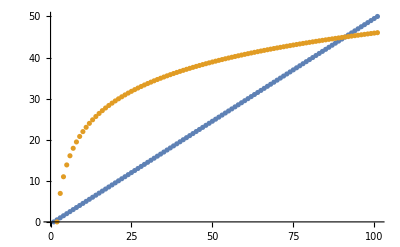

```mathematica
ListPlot[{Log[exponentialdata],Log[polynomialdata]}]
```

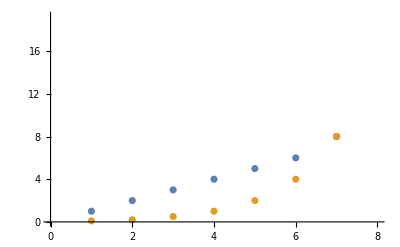

```mathematica
data1={1,2,3,4,5,6,8,100};
data2={0.1,0.2,0.5,1,2,4,8};

ListPlot[{data1,data2}]
```

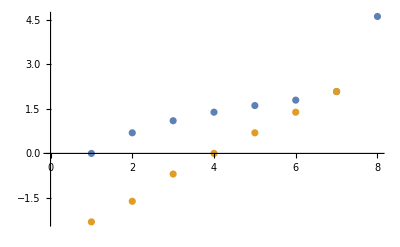

```mathematica
ListPlot[{Log[data1],Log[data2]}]
```